```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
```

```mathematica
palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)
(*Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;
```

```mathematica
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
```

```mathematica
FullSimplify[Eprey[M]]
```

29780.-997.63 M^0.09263+158.4 M^0.19

```mathematica
velocity[Mp_] := 0.33*Mp^0.21;
reactiondistance[Mp_,M_]:=0.09*(Mp*M)^0.21
EncounterRate[Mp_,M_] := velocity[Mp]*reactiondistance[Mp,M]*Cdensity
```

```mathematica
IntakeRate[Mp_,M_]:=(0.87*Mp^0.6)/Eprey[M]
```

```mathematica
FullSimplify[EncounterRate[OptPredMass[M],M]]
```

0.0263757 Cdensity M^0.21 (M^2)^0.21

```mathematica
FullSimplify[IntakeRate[OptPredMass[M],M]]
```

-(0.000736042 M^1.6)/(-29.8507 M+1. M^1.09263-0.158776 M^1.19)

```mathematica
Chat = Solve[EncounterRate[OptPredMass[M],M]==IntakeRate[OptPredMass[M],M],Cdensity]
```

{{Cdensity→(27.84 M^1.39)/((M^2)^0.21 (11316.4 M^1.+754. M^1.19+29780. (M-0.38 M^1.-0.0335 M^1.09263-0.02 M^1.19)))}}

```mathematica
ChatSol=Cdensity/.Chat[[1]]
```

(27.84 M^1.39)/((M^2)^0.21 (11316.4 M^1.+754. M^1.19+29780. (M-0.38 M^1.-0.0335 M^1.09263-0.02 M^1.19)))

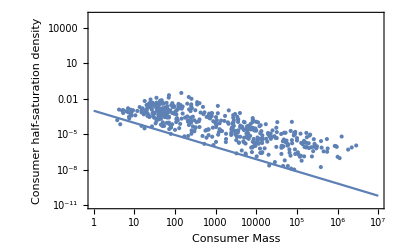

```mathematica
Show[{
LogLogPlot[(1/M)*ChatSol,{M,1,10^7},Frame->True,FrameLabel->{"Consumer Mass","Consumer half-saturation density"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}}]
}]
```

```mathematica
ChatSol/.M->10^4
```

0.00074493